# Crack the MJO Nut

## Slide Show Subtitle

Baoxiang Pan
2017.6.28

## Background

-Graphics-

Averages of all January–March MJO events from 1979–2016. Green shading shows below-average outgoing longwave radiation(wave length from 4 µm to 40 µm) values, indicating more clouds and rainfall, and brown shading identifies above-average OLR (drier and clearer skies than normal). The purple contours show the location and strength of the Pacific jet at the 200-hPa level (roughly 38,000 feet at that location). Note the eastward movement of the wet and dry areas. How far the Pacific jet extends past the international dateline also changes with the phase of the MJO. NOAA Climate.gov animation, adapted from original images provided by Carl Schreck.

```mathematica
GraphicsGrid[ArrayReshape[Import["/Users/lambda/Desktop/MJO.gif"],{4,2}],
Spacings->{10,-120},
ImageSize->Full]
```

-Graphics-

What is MJO

A remarkable feature of the atmospheric circulation and moist convection in the tropics is their tendency to be organized at planetary scales and to propagate eastward at an averaged speed of 5 m/s across the equatorial Indian and western/central Pacific oceans, with a local intraseasonal period of 30–90 days. This phenomenon  is known as the Madden-Julian Oscillation (MJO).

Tropical heat sources generate subtropical Rossby wave vorticity anomalies that are partially responsible for the retraction (extension) of the Pacific jet stream exit region and the formation of PNP anomalies

Wet (dry) events are favored during the phase of the oscillation associated with en- hanced convection near 150 E (120 E) in the tropical Pacific.

The life cycle of the MJO is characterized in this study in terms of variations in tropical convection and zonal component of the wind, specifically those that occur at the intraseasonal timescale.

To describe vari- ations in tropical convection, we use outgoing longwave radiation (OLR) data, which has been frequently used as a proxy for large-scale tropical convective activity (e.g., Lau and Chan 1986; Waliser et al. 1993; Jones et al. 1998).

The RMM index is a commonly used metric forthe observed and simulated/forecasted MJO.

MJO teleconnections in the northern extratropics.
Accurate predictions of MJO events are not sufficient
for successful subseasonal forecasts. The ability to
predict the impact of MJO events on the global circulation
is crucial.

The S2S database, a key component
of the World Weather Research Programme
(WWRP)/World Climate Research Programme
(WCRP) Subseasonal to Seasonal Prediction Project
science plan, is currently open to the public. It contains
reforecasts and also near-real-time subseasonal
to seasonal forecasts from all the major operational
centers.

desert of predictability

sudden stratospheric warmings

sudden stratospheric warming indices

The importance of the tropics in extra-tropical weather forecasting has been
illustrated by several authors. Early results from Ferranti et al. ( 1990 ) indicated that
better representation of the MJO led to better mid-latitude forecasts in the northern
hemisphere, and the benefi t of the connection of the MJO and NAO in intra- seasonal
forecasting has been demonstrated in Lin et al. ( 2010a ).

This type of I-know-it-when-I-see-it, but ill-defined situation is ripe for some machine learnin

The ensemble forecast is usually evaluated by comparing the average of the individual forecasts for one forecast variable to the observed value of that variable

Statistical diagnostics have led to a common perception that only few global models can reproduce the MJO. Here we demonstrate, using a method of tracking individual MJO events, that this perception is incorrect. Of 27 global model simulations diagnosed, all produced large-scale slowly eastward propagating signals in precipitation, which are taken as manifestations of the MJO. The difference is some model produced them frequently, others infrequently. There is no statistically significant distinction between the strength and propagation speeds of MJO events produced by most of these models. A hypothesis is proposed to interpret our results: A model can produce the MJO only in a particular background state. If the background state of a model can be constantly in a condition that is conducive to its production of the MJO, this model simulates the MJO frequently. If not, this model can still produce the MJO but only infrequently when its seasonal background state occasionally migrates into a condition that is conducive to its production of the MJO. Preliminary results from testing this hypothesis are presented

```mathematica
slat=10;
elat=32;
slon=118;
elon=135;
```

```mathematica
winter=Flatten[Table[{Range[1+i*73,24+i*73],Range[50+i*73,73+i*73]},{i,0,69}]][[1;;-25]];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/Reanalysis/NCEP/Precipitation"];
file=FileNames["*.nc"];
lat=Import[file[[1]],{"Datasets","lat"}][[slat;;elat]];
lon=Import[file[[1]],{"Datasets","lon"}][[slon;;elon]];
```

```mathematica
centers=Table[Block[{p,cp,T=20},
	p=Import[file[[i]],{"Datasets","prate"}];
	p=p[[;;,slat;;elat,slon;;elon]];
	cp=Table[Total[p[[j;;j+T-1,;;,;;]]],{j,1,Length[p]-T+1,T}];
	Map[{lat[[Position[#,Max[#]][[1,1]]]],
		 lon[[Position[#,Max[#]][[1,2]]]],
		 Max[#]}&,cp]],{i,Length[file]}];
```

```mathematica
Color[x_]:=Blend[{Red,Blue},x/0.007];
```

```mathematica
year=1954;
test=Flatten[Table[Map[#[[3]]&,centers[[i]]],{i,Length[file]}]];
ListLinePlot[test[[1+(year-1948)*73;;(year-1947)*73]],PlotRange->{20,70},ImageSize->Large]
```

-Graphics-

```mathematica
Dimensions[test]
```

{5072}

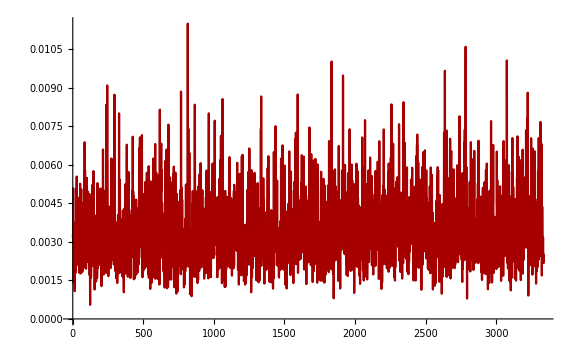

```mathematica
ListLinePlot[test[[winter]],PlotRange->Full,ImageSize->Large]
```

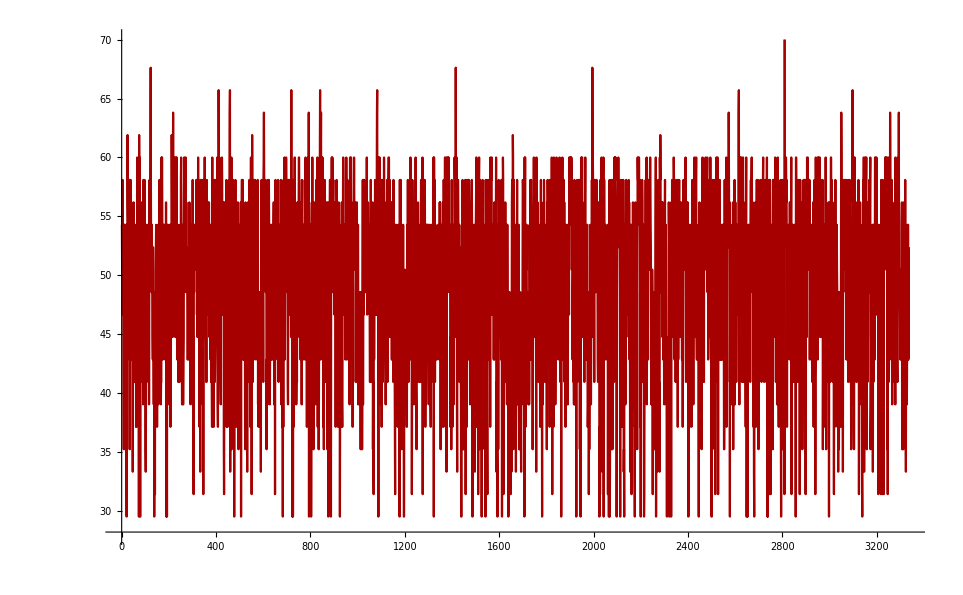

```mathematica
test=Flatten[Table[Map[#[[1]]&,centers[[i]]],{i,Length[file]}]][[winter]];
ListLinePlot[test,PlotRange->{28,70},ImageSize->Large]
```

The intrusion depth in winter is what you want to predict!!!!

```mathematica
TableForm[DFT[test]]
```

∞ | 48.8029 | 0
48.3478 | 2.34293 | 2.20909
47.6571 | 2.07248 | -0.791691
24. | 1.16225 | 0.918703
46.9859 | 0.818268 | -1.12618
556. | 0.780652 | 3.03713
3.5565 | 0.780488 | 0.406763
8.64249 | 0.633126 | -1.64983
11.0099 | 0.621963 | 1.92025
66.72 | 0.61909 | 2.10505
16.8485 | 0.618317 | -0.421109
49.0588 | 0.616238 | 2.71739
3.63795 | 0.614205 | 0.302181
16.0385 | 0.606097 | -2.81774
5.36334 | 0.605377 | 1.92889
43.3247 | 0.604478 | -0.474104
49.791 | 0.594343 | 2.32238
5.71233 | 0.593014 | -1.49148
87.7895 | 0.588496 | -0.439231
2.66454 | 0.56588 | -0.0389848
8.42424 | 0.562875 | 1.02265
3.88359 | 0.561163 | 2.52811
5.32907 | 0.554586 | -0.639785
11.7053 | 0.55335 | 2.71335
5.9254 | 0.550429 | 2.21294
8.9437 | 0.544167 | -0.206849
15.8857 | 0.543403 | -0.614301
6.87835 | 0.539686 | -2.54168
11.4639 | 0.538041 | 0.612558
45.0811 | 0.537848 | -1.5176
6.96451 | 0.537828 | -3.1266
11.957 | 0.53302 | 0.674382
62.9434 | 0.53222 | 2.40186
2.41739 | 0.527594 | 0.897203
2.68383 | 0.527572 | -0.946843
13.7851 | 0.527106 | -0.760533
2.18039 | 0.51153 | 0.497834
2.09943 | 0.511151 | 0.52702
14.5677 | 0.507803 | 2.18962
5.39806 | 0.507447 | -3.12182
370.667 | 0.504254 | -1.14752
42.7692 | 0.502224 | -0.39016
5.46885 | 0.500721 | -1.18704
11.3857 | 0.498297 | 1.64021
18.5333 | 0.497951 | -2.92864
14.696 | 0.497556 | -0.591202
3.91549 | 0.495235 | -0.331001
7.63387 | 0.493499 | -2.37194
10.2963 | 0.491615 | -1.90817
6.45261 | 0.491524 | -2.46965
3.72321 | 0.489384 | -1.20847
43.8947 | 0.487723 | -1.35192
8. | 0.486162 | 1.61267
10.2018 | 0.485935 | 0.913103
6.13235 | 0.482825 | 0.66237
18.0324 | 0.482154 | -1.11578
10.0785 | 0.48118 | 1.73094
119.143 | 0.480744 | -1.88516
3.48225 | 0.477451 | -1.00609
74.1333 | 0.474934 | 1.76661
2.32798 | 0.473535 | 2.81746
9.58621 | 0.472591 | -0.104917
10.3602 | 0.472395 | 0.662721
5.61616 | 0.47202 | 1.61962
3.53016 | 0.469625 | -2.58116
7.18966 | 0.468175 | 1.92205
7.25217 | 0.465059 | -1.88511
9.55874 | 0.464087 | -0.312557
3.94326 | 0.463936 | 0.405352
12.4944 | 0.463746 | -2.49382
2.73892 | 0.46369 | 2.18111
7.17419 | 0.463622 | -0.431943
166.8 | 0.463557 | 2.95763
6.29434 | 0.463327 | 1.45895
10.018 | 0.462446 | -0.271225
11.4247 | 0.461214 | -0.203414
29.7857 | 0.460388 | 1.40599
18.4309 | 0.46002 | -1.34851
10.6242 | 0.459678 | -0.744948
5.94652 | 0.459635 | -2.62637
5.19626 | 0.4589 | -0.246118
6.93555 | 0.458759 | 1.06535
4.11344 | 0.457442 | 0.746326
2.57805 | 0.457366 | 1.51324
5.25354 | 0.457307 | 0.84
104.25 | 0.455402 | 1.41343
10.8664 | 0.454619 | 1.85945
4.2551 | 0.450644 | -2.78316
2.52154 | 0.449766 | -0.106682
5.52318 | 0.44922 | 0.129848
9.26667 | 0.448586 | 0.499537
8.62016 | 0.448267 | -2.86662
6.42775 | 0.447527 | -2.45491
4.10837 | 0.447382 | -2.78963
7.36424 | 0.446638 | 1.45415
2.64342 | 0.442642 | -1.91942
18.8475 | 0.442178 | -1.28639
6.20074 | 0.439527 | 1.06894
2.05166 | 0.439195 | -0.178235
41.7 | 0.438123 | -1.36387
13.561 | 0.436834 | -1.73272
3.75253 | 0.435748 | -1.31222
6.10989 | 0.433742 | -0.645972
14.1356 | 0.43359 | 0.38747
4.37221 | 0.433068 | 1.82982
4.8418 | 0.432469 | 2.67611
5.83217 | 0.430676 | 0.993302
4.47185 | 0.430065 | 1.91711
20.9811 | 0.429847 | -0.154066
8.73298 | 0.427591 | 2.23964
3.12067 | 0.427266 | -1.54066
4.77253 | 0.426999 | -1.46391
6.41538 | 0.423696 | 0.0923096
4.88433 | 0.422451 | -1.74294
4.51421 | 0.422302 | 2.10912
4.74538 | 0.421731 | -2.69034
6.31818 | 0.419636 | -2.18259
4.1441 | 0.419432 | 3.03447
4.34941 | 0.419188 | 0.00940542
3.76524 | 0.418449 | -1.3041
2.53688 | 0.418411 | -1.14996
5.34615 | 0.417148 | 0.743631
2.4 | 0.413974 | 0.473615
3.26419 | 0.413742 | 2.67065
9.98802 | 0.413691 | 2.41153
3.40756 | 0.413069 | 2.51857
4.48991 | 0.41105 | 1.85573
18.9545 | 0.410952 | -2.98673
6.44015 | 0.409609 | -0.835309
5.75172 | 0.40872 | 1.74532
3.1442 | 0.407744 | -0.982515
4.41854 | 0.406531 | -1.03854
7.05285 | 0.406527 | -1.60866
3.05215 | 0.405574 | 1.6761
4.27692 | 0.405413 | 1.00843
3.01355 | 0.405192 | 0.185343
2.60422 | 0.404171 | 0.282678
14.5043 | 0.403292 | 2.11351
29.5221 | 0.40151 | 1.76075
2.95483 | 0.40142 | -1.07569
55.6 | 0.401105 | 0.486148
2.75475 | 0.401004 | -2.04751
4.05839 | 0.400412 | 2.15835
19.1724 | 0.40006 | 0.223618
5.14815 | 0.399885 | -2.28003
3.18017 | 0.399852 | -0.43094
4.18045 | 0.399568 | -1.60311
14.7611 | 0.398814 | -1.47173
14.9596 | 0.398028 | -2.23788
2.15226 | 0.397335 | 1.13087
256.615 | 0.396933 | 1.54677
2.62264 | 0.394607 | 0.678973
2.87339 | 0.394512 | 2.25186
4.40687 | 0.394422 | 2.3642
2.80101 | 0.394072 | -3.0629
2.15087 | 0.393721 | 0.840713
50.5455 | 0.39372 | 1.94041
2.82472 | 0.393159 | 1.34764
3.51899 | 0.392234 | -0.301245
2.0682 | 0.392196 | 2.78334
6.6988 | 0.39151 | 0.894282
90.1622 | 0.389685 | 2.25345
10.0482 | 0.389122 | -2.20294
3.52643 | 0.388686 | 2.77984
17.466 | 0.388514 | 1.77866
4.12361 | 0.388019 | 1.55252
2.88831 | 0.387483 | 2.36214
58.5263 | 0.387035 | 2.45405
10.902 | 0.386151 | -0.362344
2.47845 | 0.385581 | -1.4096
2.47661 | 0.385375 | 2.41236
22.5405 | 0.384764 | -2.98495
3.3663 | 0.38462 | 0.488115
3.61822 | 0.383433 | 0.36741
29.0087 | 0.382674 | -1.73684
3.99521 | 0.382321 | 0.916467
3.24514 | 0.381995 | 1.91657
3.64192 | 0.381633 | -3.01889
10.7961 | 0.38159 | -1.6084
12.9302 | 0.38125 | 0.666176
2.23742 | 0.380829 | 2.59617
14.8929 | 0.380027 | 1.22843
6.36641 | 0.378671 | 3.06546
2.00843 | 0.377624 | -2.38748
2.14534 | 0.377265 | -2.17336
5.69283 | 0.377177 | -3.1289
2.5045 | 0.376111 | -1.83386
3.46778 | 0.375796 | 0.745066
3.4321 | 0.37479 | 3.128
3.9573 | 0.373112 | -2.50884
10.1091 | 0.372468 | -1.35196
1112. | 0.37152 | -1.83882
16.7638 | 0.371268 | -2.98739
8.03855 | 0.371007 | 1.29191
12.2647 | 0.370742 | -2.65339
33.0297 | 0.370186 | -2.19538
3.46058 | 0.370026 | -0.963582
3.72737 | 0.36946 | 2.8328
3.29644 | 0.369408 | 0.43541
4.76571 | 0.369271 | -2.04522
27.3443 | 0.368828 | -2.73147
13.0824 | 0.368721 | -0.13733
3.95261 | 0.368706 | 1.83926
7.77622 | 0.36851 | 2.35428
2.27713 | 0.367154 | -0.0176221
2.52536 | 0.365605 | 1.84905
2.58204 | 0.365428 | 1.74072
7.92399 | 0.365418 | 0.99374
2.57606 | 0.365361 | 2.02546
3.92471 | 0.365042 | 1.54687
5.98923 | 0.364052 | 1.32871
2.61852 | 0.363738 | 1.0559
5.54153 | 0.362814 | 2.23057
2.4209 | 0.362781 | 2.4945
4.28241 | 0.362641 | 2.63436
8.55385 | 0.361876 | 2.91528
15.3733 | 0.3602 | -1.90139
2.0863 | 0.360135 | -2.19753
2.29278 | 0.358793 | -2.22793
7.03797 | 0.358329 | -3.13485
3.03825 | 0.357183 | 3.10644
6.90683 | 0.356945 | 2.38853
2.03663 | 0.356775 | 0.439891
3.05495 | 0.356748 | -0.477881
6.672 | 0.356722 | -1.35688
12. | 0.3565 | 1.77603
3.47138 | 0.356395 | 2.78238
21.6623 | 0.356316 | 0.620954
7.28384 | 0.3552 | 1.12661
2.30705 | 0.354956 | 1.14501
22.24 | 0.354744 | 2.09644
2.11139 | 0.354547 | 0.700897
28.2712 | 0.354359 | 1.48315
15.9617 | 0.354027 | 0.325156
3.35952 | 0.353822 | 1.50072
3336. | 0.352661 | -0.206614
4.12871 | 0.352625 | 2.92311
6.80816 | 0.352498 | 0.505803
10.6923 | 0.352169 | 1.88778
2.16342 | 0.351003 | -1.42093
3.31281 | 0.350145 | -1.52719
3.84332 | 0.349958 | -3.12636
4.98655 | 0.349743 | -2.84568
2.21809 | 0.349595 | 0.979813
4.80692 | 0.349209 | -1.57949
8.17647 | 0.348759 | -0.744012
3.57556 | 0.348514 | 2.85113
20.7205 | 0.347383 | 1.24591
2.9627 | 0.347109 | 2.66496
3.069 | 0.347085 | -0.205634
3.69027 | 0.347074 | -0.804373
4.39526 | 0.347018 | -0.42401
5.06222 | 0.347007 | -1.57036
30.3273 | 0.346988 | -1.25052
19.5088 | 0.346795 | 0.616262
3.06336 | 0.346676 | 0.535587
2.19908 | 0.346653 | 2.18354
39.2471 | 0.346645 | 0.331648
6.72581 | 0.34634 | -0.573535
4.65272 | 0.346047 | -2.7629
2.04914 | 0.345698 | -1.55276
14.4416 | 0.345157 | -1.23005
18.3297 | 0.344945 | -1.46897
5.5786 | 0.344696 | 1.45501
10.1398 | 0.344282 | -2.5041
15.5888 | 0.343782 | 0.291616
5.87324 | 0.34287 | -2.02588
2.71883 | 0.342636 | -2.78842
4.92035 | 0.342557 | 2.24327
3.76099 | 0.342446 | 2.04824
44.48 | 0.342118 | 0.0186989
2.86598 | 0.341217 | 3.07444
9.13973 | 0.340876 | -0.0104738
5.07763 | 0.340118 | -2.31711
95.3143 | 0.339858 | 1.78841
10.1707 | 0.33893 | 2.85204
4.93491 | 0.338268 | 0.29204
10.2331 | 0.338162 | -1.09571
2.73219 | 0.336952 | -0.264734
37.0667 | 0.336495 | 0.248118
4.08323 | 0.335905 | -2.68103
2.14396 | 0.335605 | 1.84963
15.1636 | 0.334944 | 1.14791
2.16905 | 0.334839 | 0.314399
4.43028 | 0.33314 | 1.02759
3.71079 | 0.333109 | 2.81423
3.07749 | 0.333043 | 0.179178
54.6885 | 0.332377 | -0.27209
2.15922 | 0.332222 | 2.6192
2.02182 | 0.331638 | 1.20804
2.085 | 0.331331 | -3.11658
7.75814 | 0.330931 | -1.98268
2.42795 | 0.330545 | 1.08917
12.9805 | 0.330355 | -0.309872
30.6055 | 0.330004 | 0.756639
9.04065 | 0.329822 | -3.10877
3.15909 | 0.329757 | 0.0954858
2.18611 | 0.329528 | 2.93981
4.26054 | 0.328584 | -0.866203
52.125 | 0.328218 | 1.11991
25.2727 | 0.328092 | -2.7686
2.55241 | 0.327443 | 2.99415
6.34221 | 0.327082 | 0.915876
8.40302 | 0.327047 | -2.90693
123.556 | 0.32628 | 0.360656
24.7111 | 0.326071 | -0.68751
2.51016 | 0.325673 | -1.49612
60.6545 | 0.325338 | -1.571
2.25405 | 0.325087 | -2.24429
3.62609 | 0.324435 | -0.752237
4.50811 | 0.324336 | -2.6451
2.97857 | 0.324299 | -1.8972
4.04854 | 0.323907 | 2.20863
2.42442 | 0.323671 | -3.05109
2.70779 | 0.322996 | 2.47547
2.06436 | 0.321965 | -2.67386
6.40307 | 0.321455 | 2.02766
2.21514 | 0.320538 | 1.52974
2.88581 | 0.320506 | 2.93035
11.788 | 0.319435 | -2.63436
7.0678 | 0.319228 | -2.79277
5.28685 | 0.319118 | 1.04784
4.52033 | 0.319101 | 2.94927
17.7447 | 0.318908 | -2.55542
14.3793 | 0.318384 | 2.5324
2.1034 | 0.31814 | -2.42284
2.11675 | 0.317696 | 1.32144
6.03255 | 0.317502 | -1.89862
3.23569 | 0.317273 | -0.939957
5.0015 | 0.317148 | -1.84943
4.53878 | 0.316826 | 2.54262
2.03291 | 0.316575 | 0.380142
17.375 | 0.316557 | 1.0718
16.1159 | 0.316323 | -2.32548
2.53303 | 0.316316 | -2.09927
2.0837 | 0.316024 | 1.15029
2.48584 | 0.315835 | -0.128308
2.93146 | 0.315305 | -0.666684
6.83607 | 0.315302 | 1.12812
3.18929 | 0.314859 | 0.334715
7.42984 | 0.314479 | -0.654397
17.6508 | 0.313901 | 1.68372
5.8836 | 0.313455 | -1.08793
42.2278 | 0.313453 | -1.88085
16.2732 | 0.313212 | 1.79281
222.4 | 0.313128 | 0.16251
11.8719 | 0.313044 | 0.013182
2.76846 | 0.311928 | -3.05002
4.94955 | 0.311621 | -2.1422
3.5042 | 0.31162 | -1.67953
36.2609 | 0.311415 | 2.16003
3.5603 | 0.311159 | -2.2461
3.35614 | 0.310855 | 0.96159
23.1667 | 0.310624 | -1.51183
5.68313 | 0.31027 | 0.839393
17.285 | 0.310165 | 2.21395
2.00601 | 0.310102 | 2.32366
2.34105 | 0.30983 | 0.0150997
3.85219 | 0.309821 | -1.95564
3.22631 | 0.309621 | 3.01054
13.6721 | 0.309615 | -3.00133
5.15611 | 0.309349 | 0.546602
16.1942 | 0.309263 | 1.62355
3.962 | 0.309241 | 1.47358
9.06522 | 0.309215 | 1.99785
2.86844 | 0.308544 | 2.34669
1668. | 0.308355 | -2.70828
6.27068 | 0.308345 | 3.0458
4.92762 | 0.30823 | -0.376906
3.71906 | 0.307928 | -2.55986
6.65868 | 0.307767 | -2.16077
2.76388 | 0.307595 | 2.67849
196.235 | 0.307447 | -0.0941642
12.2198 | 0.30692 | 1.78189
22.0927 | 0.306728 | 1.89024
2.06691 | 0.306042 | 1.70592
4.58872 | 0.305876 | 1.76641
9.53143 | 0.305748 | -2.97036
4.20151 | 0.305375 | -0.139581
7.23644 | 0.304842 | 2.26998
2.95221 | 0.30448 | 1.85352
2.59813 | 0.304423 | 1.82751
2.0824 | 0.304372 | 1.23817
4.53261 | 0.30421 | -1.07138
5.55075 | 0.30415 | 1.67116
72.5217 | 0.303587 | -2.82564
9.37079 | 0.303472 | 1.96487
18.1304 | 0.30265 | 3.03335
2.57011 | 0.302249 | -1.91367
3.78231 | 0.302028 | 0.658447
834. | 0.301701 | 1.99907
32.0769 | 0.30163 | -1.55293
4.82779 | 0.301511 | 1.64472
2.99461 | 0.301261 | 1.37222
2.80808 | 0.30121 | 2.63705
3.45342 | 0.301207 | -2.34533
2.2122 | 0.301171 | -1.69859
68.0816 | 0.301067 | 2.87517
2.53111 | 0.300953 | 0.418911
2.10739 | 0.300615 | -1.04617
3.87007 | 0.300044 | 0.598488
3.81257 | 0.300014 | -0.247575
12.7816 | 0.299672 | 2.20624
21.2484 | 0.299571 | 1.8835
5.49588 | 0.299304 | -1.37381
12.5887 | 0.298955 | -2.55401
2.77076 | 0.298828 | 1.017
4.61411 | 0.298452 | 2.42402
2.41914 | 0.298408 | -2.97838
4.19095 | 0.298394 | -1.07876
5.0469 | 0.298374 | 0.928752
3.15312 | 0.298307 | -0.399383
4.55738 | 0.297942 | -1.73464
2.48955 | 0.297019 | -2.52201
11.7465 | 0.296867 | 0.306939
11.1572 | 0.296502 | 3.08981
19.6235 | 0.296488 | 2.33722
3.68212 | 0.296317 | 0.769664
4.04364 | 0.296229 | -2.94307
17.1959 | 0.29622 | 1.6386
3.73572 | 0.295354 | -2.60706
8.71018 | 0.295237 | 1.46867
6.0765 | 0.294549 | -1.93645
11.2323 | 0.294172 | 1.59583
5.97849 | 0.294165 | 1.37197
12.7328 | 0.294147 | 1.99798
3.43918 | 0.2941 | -0.535933
3.88811 | 0.293972 | -3.10733
2.49888 | 0.293478 | -3.07211
2.65183 | 0.293401 | -2.19414
7.1588 | 0.293096 | -1.21377
3.44984 | 0.292866 | 1.92661
2.10872 | 0.291889 | 0.163842
61.7778 | 0.291506 | -1.81916
3.0438 | 0.291461 | 1.04815
3.85665 | 0.291064 | -2.98142
3.44272 | 0.290979 | 1.09669
4.05346 | 0.290427 | -1.86794
3.55272 | 0.290197 | -1.92596
45.6986 | 0.289885 | -0.380322
6.64542 | 0.289754 | -2.24492
2.97061 | 0.289751 | -1.64287
3.34269 | 0.289614 | -1.57371
19.976 | 0.28954 | -2.74563
2.39483 | 0.289483 | -1.61906
12.8308 | 0.289162 | 2.34944
3.54894 | 0.288613 | -0.807343
3.62215 | 0.288592 | -1.55202
6.37859 | 0.288442 | -2.28362
34.75 | 0.288391 | -0.853188
8.896 | 0.287908 | 2.96794
7.58182 | 0.286862 | 1.75414
4.56986 | 0.286829 | -1.42132
7.51351 | 0.28682 | 1.77946
8.11679 | 0.286422 | -0.129441
2.98123 | 0.286221 | -1.16841
2.23293 | 0.285486 | -0.159806
5.63514 | 0.284932 | 2.95067
8.27792 | 0.284872 | 2.43816
2.68167 | 0.284858 | -2.37328
4.69859 | 0.284566 | -1.92046
2.9839 | 0.284441 | -2.97808
2.18325 | 0.28395 | -2.39355
8.34 | 0.283555 | -2.06193
2.45836 | 0.282677 | 1.23196
10.7613 | 0.282653 | -2.85639
3.09175 | 0.282556 | 0.0182344
2.81757 | 0.282087 | -0.325658
4.77937 | 0.281994 | 3.12626
2.34599 | 0.281917 | -0.0733773
2.02673 | 0.281733 | 0.244865
2.23443 | 0.281658 | 1.90313
13.344 | 0.281537 | 0.0214371
3.07182 | 0.281536 | 3.06448
10.5905 | 0.281519 | -1.49204
2.90592 | 0.281357 | 1.83323
13.2908 | 0.281253 | 2.04814
25.4656 | 0.281246 | -0.331227
2.56813 | 0.280949 | -2.46999
5.3121 | 0.280839 | 0.27659
4.70522 | 0.280694 | 2.42872
15.7358 | 0.280654 | -2.16354
17.8396 | 0.28064 | -1.01316
2.74342 | 0.280053 | 2.58901
2.03539 | 0.280031 | -1.6384
34.3918 | 0.279797 | 3.09803
6.71227 | 0.279219 | 2.12985
2.69903 | 0.2791 | 1.20177
2.39655 | 0.278966 | -0.510814
3.3194 | 0.278678 | -1.76251
2.77537 | 0.278288 | 0.198321
9.16484 | 0.278276 | 2.68645
417. | 0.278225 | -2.42572
10.9377 | 0.278125 | -0.328709
4.63333 | 0.2781 | -0.65878
3.51158 | 0.277964 | 2.15861
8.3609 | 0.277398 | -1.7126
2.38456 | 0.277202 | 1.07371
8.3192 | 0.276541 | 0.895238
3.3629 | 0.276533 | -0.942384
3.3697 | 0.276265 | -1.02824
3.80388 | 0.276051 | -1.7687
4.43617 | 0.275995 | 2.36553
8.84881 | 0.275807 | -0.025498
4.36649 | 0.275256 | 1.20103
26.2677 | 0.275008 | 0.549875
4.58242 | 0.274842 | -2.75481
3.46417 | 0.274678 | -0.476658
5.24528 | 0.274492 | -0.288283
6.09872 | 0.274386 | 0.542031
5.70256 | 0.274069 | 2.04594
2.17046 | 0.2729 | -2.40907
9.01622 | 0.272782 | 1.11842
4.0048 | 0.272137 | -1.54818
2.37607 | 0.271533 | 2.84188
2.83432 | 0.271348 | -2.51177
22.3893 | 0.271179 | -0.959907
2.30069 | 0.271177 | -2.20844
2.45114 | 0.271118 | 1.54029
2.30387 | 0.270701 | 1.11526
5.4599 | 0.270618 | -2.22675
21.5226 | 0.270437 | 2.9961
2.23592 | 0.270022 | -1.7427
5.40681 | 0.2699 | -3.13562
20.4663 | 0.269827 | 0.679678
6.97908 | 0.269776 | 1.15297
2.30546 | 0.269758 | 1.87396
3.43563 | 0.269743 | -1.19182
4.33247 | 0.269557 | 1.22774
5.48684 | 0.269547 | -1.21716
4.68539 | 0.269386 | -1.62187
8.15648 | 0.269362 | -1.04974
2.12349 | 0.268511 | 1.03349
2.54075 | 0.268332 | 1.89102
4.4127 | 0.268301 | 0.214122
3.63399 | 0.268153 | 2.72927
2.69685 | 0.268005 | -0.459179
2.09548 | 0.26799 | 2.76119
2.25863 | 0.26795 | -1.06072
2.3345 | 0.267724 | 0.875433
4.66573 | 0.26758 | -1.24179
151.636 | 0.267461 | 2.83314
7.86792 | 0.267444 | 0.647556
2.70121 | 0.267004 | 0.0477315
2.72327 | 0.266964 | -2.03249
2.09679 | 0.266945 | -1.81655
4.90588 | 0.266409 | 1.1157
4.22278 | 0.266207 | 2.16936
2.38968 | 0.266082 | -1.99178
2.64762 | 0.265885 | -0.848271
23.493 | 0.265859 | -0.834529
3.93396 | 0.265766 | 1.28172
12.1752 | 0.265395 | 0.0232603
53.8065 | 0.265346 | 1.82083
4.02413 | 0.265294 | -3.00781
3.05775 | 0.265198 | 0.605031
2.75931 | 0.265056 | -2.40992
30.0541 | 0.264935 | 1.25967
5.22066 | 0.26402 | 2.48833
4.24427 | 0.263554 | -2.3872
2.38116 | 0.26298 | -1.53647
2.83192 | 0.262916 | -1.61958
12.4015 | 0.262694 | 1.96215
9.95821 | 0.262393 | 2.4963
3.74831 | 0.262349 | 2.71633
5.72213 | 0.261978 | 1.27617
2.35593 | 0.261952 | -0.974792
8.57584 | 0.26189 | -0.519025
4.03386 | 0.261819 | -0.108417
7.88652 | 0.261739 | -2.92171
2.13436 | 0.261507 | 1.53868
4.07326 | 0.261492 | 2.33034
4.40106 | 0.261031 | -0.772931
2.43682 | 0.260924 | 0.0744672
9.34454 | 0.260706 | 2.68376
6.24719 | 0.260416 | -0.392945
3.84775 | 0.260416 | -0.209578
3.79954 | 0.260207 | 2.1416
2.75021 | 0.259939 | -2.95981
9.47727 | 0.259858 | 1.98646
6.99371 | 0.259848 | -0.55779
111.2 | 0.259847 | 1.8021
3.13829 | 0.259764 | 1.16964
19.8571 | 0.259656 | 2.69421
36.6593 | 0.259239 | -2.3984
10.4577 | 0.25883 | 2.16807
3.41104 | 0.258781 | 0.840934
2.05292 | 0.258129 | 3.01203
4.448 | 0.257569 | 0.258791
27.122 | 0.25756 | 0.26896
6.18924 | 0.2575 | -2.44656
2.17329 | 0.25727 | 2.54683
2.00964 | 0.256922 | -2.25928
3.01083 | 0.25646 | -0.192428
3.47862 | 0.256327 | -2.31781
2.07592 | 0.256232 | -2.48704
33.36 | 0.255845 | -0.306236
15.4444 | 0.255756 | 2.6822
5.06991 | 0.25574 | 0.366139
3.71492 | 0.255518 | 1.82321
2.92632 | 0.255476 | 1.07551
2.4803 | 0.25524 | 2.96429
3.59483 | 0.255139 | -2.32974
32.3883 | 0.255126 | -2.32948
4.38371 | 0.254062 | -0.146766
2.55632 | 0.253806 | -0.0578115
6.05445 | 0.253738 | 0.353982
3.66997 | 0.253735 | -1.29875
6.21229 | 0.253646 | 0.316731
28.0336 | 0.253545 | 1.68801
2.99193 | 0.25354 | 0.555299
3.86559 | 0.253418 | 0.11559
3.22943 | 0.253277 | -2.12695
2.18182 | 0.253193 | -0.928691
19.3953 | 0.252933 | -1.81887
3.16209 | 0.252524 | -1.09383
4.03874 | 0.25228 | 1.42754
6.51563 | 0.252227 | 0.0372979
33.697 | 0.252149 | 0.614028
5.12442 | 0.25209 | 0.801425
2.02304 | 0.251917 | -1.43617
2.18754 | 0.251852 | -0.280112
24.1739 | 0.251662 | 1.83423
5.13231 | 0.25147 | -1.37001
7.44643 | 0.251058 | 2.80841
11.5833 | 0.251048 | 2.35898
2.26939 | 0.251034 | 0.130773
2.72772 | 0.250758 | 0.0154695
3.80822 | 0.250749 | 0.325939
6.35429 | 0.250516 | -2.75995
40.1928 | 0.250275 | 2.68747
11.6237 | 0.250274 | 1.79625
35.4894 | 0.24991 | 0.587324
3.60649 | 0.249903 | -2.95545
2.0798 | 0.249641 | 0.445527
2.81995 | 0.24964 | 0.622938
3.17412 | 0.249562 | -0.416427
2.31828 | 0.249373 | 1.96775
3.01627 | 0.249268 | -0.832603
4.8559 | 0.248666 | -0.693865
2.32636 | 0.24851 | 2.38409
2.75702 | 0.248506 | -0.99081
3.11776 | 0.248402 | 0.400258
7.98086 | 0.247988 | 0.971596
4.6205 | 0.247932 | -2.82387
2.0255 | 0.247605 | 0.725739
3.9109 | 0.247462 | 2.40331
2.65394 | 0.247357 | -0.550616
3.77376 | 0.247226 | 2.32822
2.68815 | 0.247065 | -0.544716
2.41215 | 0.247003 | -2.65408
3.33934 | 0.246938 | -0.955516
4.8 | 0.246773 | 2.17451
6. | 0.246291 | 0.502731
13.0313 | 0.246087 | 1.8289
2.81519 | 0.246086 | -0.493404
2.11944 | 0.246067 | 1.45424
5.10092 | 0.245911 | -2.08614
333.6 | 0.245487 | -2.54689
4.34375 | 0.245242 | -0.830765
69.5 | 0.245181 | 0.334685
2.44217 | 0.244754 | -2.41282
8.48855 | 0.244503 | -0.365867
3.22008 | 0.244428 | -0.729694
2.84399 | 0.244406 | -1.90259
3.1954 | 0.244392 | -2.49238
9.50427 | 0.244392 | -0.172713
2.06053 | 0.244238 | 1.40615
2.7122 | 0.244035 | -1.16786
2.9973 | 0.243842 | 0.829698
2.80336 | 0.243839 | 1.43876
4.87007 | 0.243519 | -2.38417
3.25463 | 0.243404 | 3.11135
4.10332 | 0.243358 | -1.39099
2.05545 | 0.243134 | 1.2023
2.76617 | 0.243102 | 1.00326
29.2632 | 0.242871 | -0.121998
2.29752 | 0.242822 | -1.03505
3.3868 | 0.242715 | 1.57081
4.20681 | 0.242132 | -0.436536
21.9474 | 0.241905 | 2.44914
4.60138 | 0.241702 | 0.755037
2.85372 | 0.24151 | -2.9337
3.27059 | 0.24134 | -0.698485
2.98657 | 0.240997 | -2.39526
3.02722 | 0.240699 | -1.90483
7.81265 | 0.240495 | -1.6467
3.67401 | 0.240466 | -0.821697
8.05797 | 0.240013 | 1.4456
4.56361 | 0.239996 | 0.109192
2.31345 | 0.239893 | -2.64734
2.90087 | 0.239811 | 1.85671
26.0625 | 0.239685 | -2.66482
37.9091 | 0.239284 | 0.443605
7.72222 | 0.239172 | 0.348204
5.41558 | 0.238911 | -0.583343
3.50789 | 0.23876 | 1.08178
3.66191 | 0.238749 | 1.55106
2.15365 | 0.238103 | -1.92924
3.61039 | 0.237933 | 2.66599
6.23551 | 0.237216 | 0.771846
2.22697 | 0.236432 | 2.22214
4.01444 | 0.23642 | 0.417231
3.16509 | 0.236321 | -0.703975
4.45394 | 0.23613 | -1.90472
11.8298 | 0.235808 | -1.00148
4.31565 | 0.235733 | 0.448425
7.46309 | 0.235707 | 0.289448
3.82131 | 0.235586 | 1.10083
2.15504 | 0.235563 | -2.09002
5.18818 | 0.235466 | -1.49867
9.81176 | 0.235043 | 2.53249
2.68599 | 0.234508 | 2.6821
5.03167 | 0.234328 | -1.98076
19.2832 | 0.234203 | -0.059976
2.33941 | 0.233737 | 2.08238
3.51528 | 0.233531 | -0.968215
4.87719 | 0.233515 | -0.0305738
3.77803 | 0.233438 | 0.0434637
4.48387 | 0.233366 | 0.597897
2.34764 | 0.232403 | 1.13137
5.10873 | 0.232353 | -0.332131
12.5414 | 0.232173 | -0.453143
12.6844 | 0.232118 | -2.06713
9.42373 | 0.23201 | 2.18286
2.40693 | 0.231807 | 0.0178344
6.82209 | 0.231605 | -0.356217
2.0012 | 0.231511 | -0.589147
3.06618 | 0.231321 | -0.82415
8.5102 | 0.231107 | -2.12623
2.87091 | 0.230887 | 1.39001
9.241 | 0.230697 | 1.46367
3.54516 | 0.230553 | -1.25649
6.33017 | 0.23043 | -0.214453
2.10606 | 0.230313 | -1.91589
2.93404 | 0.230281 | 0.00393849
3.92933 | 0.230274 | -2.89076
4.09325 | 0.229881 | 2.4527
2.89583 | 0.229761 | -1.69817
3.79522 | 0.229721 | -0.485671
5.59732 | 0.229627 | 2.02826
8.87234 | 0.229576 | 1.91202
7.14347 | 0.229375 | 2.47703
6.89256 | 0.229019 | -0.182139
9.11475 | 0.228829 | -1.98474
2.27558 | 0.228701 | 0.912049
9.64162 | 0.228478 | -3.0282
3.26738 | 0.228372 | -1.55223
3.11194 | 0.227928 | -1.22728
667.2 | 0.227851 | -0.400953
2.51774 | 0.227721 | 2.02504
7.33187 | 0.226998 | -0.485394
2.67308 | 0.226592 | -2.68744
6.57988 | 0.226413 | 2.37072
11.2703 | 0.226177 | -2.57277
4.97168 | 0.225958 | -1.61617
4.82081 | 0.225891 | -2.74934
2.13572 | 0.225715 | 3.0723
2.04412 | 0.225582 | 1.9409
3.5339 | 0.225498 | 2.92208
18.7416 | 0.225478 | 2.6663
4.67882 | 0.225447 | 0.273598
26.688 | 0.225265 | 1.81968
2.53881 | 0.224947 | 1.27773
4.15442 | 0.224856 | -0.112824
2.03415 | 0.224579 | -0.692593
4.83478 | 0.224485 | -1.3789
5.58794 | 0.224405 | -2.3758
10.557 | 0.224357 | 2.01279
2.88332 | 0.223686 | -0.640459
2.44754 | 0.223608 | 2.89334
6.22388 | 0.223293 | -2.41572
4.75214 | 0.222407 | 1.64491
81.3659 | 0.222223 | 0.0740532
8.46701 | 0.22216 | -1.00889
16.4335 | 0.222066 | 0.766568
2.43504 | 0.221855 | -2.78853
6.50292 | 0.221812 | -2.30495
9.92857 | 0.221772 | 2.22459
2.27248 | 0.221338 | 1.5134
6.60594 | 0.221197 | -2.60596
9.45042 | 0.221196 | -1.21466
3.336 | 0.221077 | -0.026537
2.09154 | 0.220634 | 1.95909
5.00901 | 0.220432 | 0.376559
13.5061 | 0.220338 | -1.91472
2.58805 | 0.22033 | 1.6013
2.50263 | 0.220276 | 1.94301
3.2738 | 0.220039 | -1.89793
7.94286 | 0.219981 | 0.716629
4.23888 | 0.219647 | -0.205501
4.19623 | 0.219309 | 0.625365
14.6316 | 0.219028 | 2.45911
3.13534 | 0.218963 | 1.5342
2.92119 | 0.218849 | -2.81859
3.65789 | 0.218756 | -0.229752
13.8423 | 0.218408 | -0.955516
2.50075 | 0.217781 | -1.32074
7.66897 | 0.217585 | 1.33473
4.38947 | 0.217376 | 0.0354581
5.51405 | 0.217369 | -0.380855
2.04162 | 0.217307 | -1.70955
2.98925 | 0.217105 | -2.41887
3.06055 | 0.216917 | -0.62992
6.1211 | 0.216897 | 0.210147
3.39715 | 0.216892 | 2.70692
3.3161 | 0.216825 | 1.74889
2.20053 | 0.216639 | -3.10243
4.50202 | 0.216612 | -2.08342
5.53234 | 0.216443 | -2.20651
23.6596 | 0.216441 | -1.3435
3.5414 | 0.216347 | 0.282421
2.26016 | 0.216001 | 3.00334
34.0408 | 0.215946 | -1.00945
2.23144 | 0.215677 | -0.731005
2.84885 | 0.215622 | -0.790598
2.01328 | 0.215354 | -0.688281
10.3925 | 0.215235 | -2.72671
8.99191 | 0.215166 | -2.6256
2.37946 | 0.215017 | 0.89801
3.02174 | 0.21427 | -2.38077
11.3469 | 0.213576 | -2.48915
2.12891 | 0.213529 | -0.394244
5.56928 | 0.213411 | 0.514947
10.3282 | 0.213384 | 2.57952
5.74182 | 0.213107 | 0.729692
2.41389 | 0.21285 | 1.64482
7.74014 | 0.212775 | 2.78002
7.90521 | 0.212522 | -2.93728
3.04102 | 0.212428 | -1.21219
2.66667 | 0.212359 | 0.0396629
6.54118 | 0.212337 | 2.93111
7.54751 | 0.212057 | -1.18358
4.3381 | 0.212053 | 1.93252
2.3914 | 0.211746 | -1.35113
12.1309 | 0.211326 | -0.126864
2.17755 | 0.211134 | 2.47763
15.095 | 0.210875 | 1.57122
4.52646 | 0.210785 | -1.79212
3.28994 | 0.210779 | -0.0556232
2.19763 | 0.210772 | -3.1044
7.11301 | 0.210462 | -0.122852
2.04037 | 0.210416 | 0.788108
2.20927 | 0.210101 | -2.65952
2.25253 | 0.209951 | -3.00733
4.7931 | 0.209939 | 2.65076
13.4516 | 0.209691 | -0.510007
2.97326 | 0.209467 | 1.17424
3.73154 | 0.20919 | -1.24651
3.3731 | 0.209108 | 2.7802
4.96429 | 0.208837 | -0.228091
2.3427 | 0.208558 | 0.541536
2.67952 | 0.20837 | -2.25832
4.69198 | 0.208225 | 2.0558
2.61442 | 0.208022 | -0.767922
13.9 | 0.207722 | -1.90844
5.44209 | 0.207657 | -2.28197
16.3529 | 0.20753 | -1.20487
2.73667 | 0.207517 | -2.33324
8.59794 | 0.20751 | -1.51354
3.50052 | 0.207479 | -3.13257
2.17613 | 0.207422 | 0.215348
3.98091 | 0.207372 | 1.27006
5.62563 | 0.207357 | 0.611689
2.58005 | 0.20711 | -1.77924
4.94222 | 0.207028 | 0.990843
17.9355 | 0.206713 | -1.2224
2.1481 | 0.206693 | -1.19532
3.16809 | 0.206662 | -1.70314
2.31025 | 0.206608 | 0.389065
4.31008 | 0.206322 | -1.3521
9.75439 | 0.206236 | 0.915716
2.20198 | 0.205807 | -2.82533
4.21745 | 0.205775 | -1.1322
5.78163 | 0.205758 | 2.41325
3.18625 | 0.205645 | -1.9029
2.13299 | 0.205519 | 2.73776
2.947 | 0.205426 | 1.51405
7.59909 | 0.20528 | -2.57392
31.1776 | 0.205253 | 2.1798
5.84238 | 0.205144 | 2.41995
4.08824 | 0.204796 | -0.374235
303.273 | 0.204537 | 2.64553
2.79397 | 0.204354 | -2.44526
133.44 | 0.204347 | 3.08615
2.17897 | 0.204043 | -2.48723
2.12484 | 0.203945 | 2.59868
6.59289 | 0.203769 | -0.0534111
2.0024 | 0.203495 | 2.25989
3.90175 | 0.203335 | -0.00847073
2.72549 | 0.203076 | -1.64496
7.34802 | 0.202949 | 0.526187
3.04936 | 0.202926 | 1.2751
2.28025 | 0.202887 | 2.06925
4.1596 | 0.202498 | -1.22103
2.0292 | 0.202199 | 0.462654
4.29344 | 0.201192 | 2.69118
4.71186 | 0.201173 | 0.0293813
2.12079 | 0.201123 | -2.31804
2.72995 | 0.201092 | -0.0925259
2.7893 | 0.20063 | 1.9799
2.22104 | 0.200265 | 2.59228
2.62677 | 0.200193 | -1.80219
5.91489 | 0.200069 | -1.50109
2.07463 | 0.199967 | -1.48979
7.61644 | 0.199755 | -2.11192
30.8889 | 0.199627 | 2.20539
2.04537 | 0.198975 | -0.854387
98.1176 | 0.198953 | 1.94278
3.14124 | 0.198923 | -0.480618
4.73191 | 0.198904 | 0.130651
6.7943 | 0.198897 | 2.85223
2.02059 | 0.198679 | -0.0458143
14.3176 | 0.198666 | -1.25767
2.55828 | 0.19811 | -3.14017
3.87907 | 0.198059 | -3.09236
5.03927 | 0.197787 | -1.34875
2.15783 | 0.197514 | 1.27548
128.308 | 0.19738 | 2.20633
2.19474 | 0.197328 | -2.23621
6.30624 | 0.197292 | -0.364094
2.69467 | 0.197262 | -2.97895
2.54656 | 0.197152 | -2.4736
13.3976 | 0.197115 | -0.802651
38.3448 | 0.19685 | 0.756498
2.2865 | 0.196586 | -2.54382
10.8312 | 0.196474 | 0.913205
3.90632 | 0.196328 | 2.09162
2.30228 | 0.195735 | -0.0280802
10.4906 | 0.195449 | -3.04406
5.27014 | 0.195401 | 1.13946
2.30865 | 0.195069 | -0.717069
5.30366 | 0.194641 | 0.0786458
4.86297 | 0.194499 | 2.48498
3.49686 | 0.194477 | -0.560421
2.05799 | 0.194146 | 3.09452
23.0069 | 0.193956 | -0.941883
2.51394 | 0.193907 | -2.71075
7.0828 | 0.193735 | -3.06857
2.09285 | 0.19371 | 0.108795
2.97591 | 0.193243 | -1.7335
2.6247 | 0.192756 | 1.69257
7.09787 | 0.192496 | 2.50784
2.67522 | 0.192296 | -0.875656
7.70439 | 0.192099 | -1.49239
20.2182 | 0.192067 | 0.35761
3.20461 | 0.191713 | 1.64511
2.14258 | 0.19122 | -1.90108
2.91354 | 0.191027 | 2.97824
2.86352 | 0.190755 | -1.55112
9.72595 | 0.190255 | -2.51154
14.8267 | 0.190234 | -0.782715
2.34434 | 0.190005 | -1.56022
3.3494 | 0.189874 | -1.49982
2.05672 | 0.18951 | 1.8065
18.2295 | 0.18942 | 0.409178
2.46563 | 0.189403 | 0.154075
19.0629 | 0.189362 | -1.90117
28.5128 | 0.189007 | -0.0721977
2.26323 | 0.18869 | 1.14162
2.96797 | 0.188662 | -0.107772
9.69767 | 0.188646 | -2.71555
2.0811 | 0.188593 | 0.561174
208.5 | 0.188464 | -2.9652
3.27701 | 0.188431 | -2.30538
3.42505 | 0.188226 | 1.64131
9.78299 | 0.188071 | -2.30724
3.76949 | 0.188008 | 2.71943
2.36764 | 0.187836 | 1.19185
3.73991 | 0.187485 | 2.72833
11.1946 | 0.187404 | 2.43579
3.40408 | 0.187092 | -2.83613
2.26477 | 0.186996 | -1.54049
2.47111 | 0.186035 | 0.00951032
3.79091 | 0.185979 | -0.66943
2.22252 | 0.185927 | 0.183269
2.19041 | 0.185769 | -1.50557
11.9143 | 0.185497 | -0.124676
2.92888 | 0.185433 | 0.892821
5.79167 | 0.185194 | 0.206661
18.6369 | 0.185131 | -2.88205
5.76166 | 0.184665 | -0.478091
4.81385 | 0.184393 | 2.18278
2.53495 | 0.184295 | 0.120836
2.25558 | 0.184266 | 2.69497
3.5641 | 0.184215 | 2.99188
2.61237 | 0.184174 | -1.98447
7.68664 | 0.184093 | -0.920123
3.28024 | 0.183829 | 2.3951
57.5172 | 0.183744 | 0.456159
4.9791 | 0.183376 | -0.31732
2.24344 | 0.183374 | -2.28927
4.29897 | 0.183365 | 1.3833
2.95745 | 0.183296 | 0.173493
2.59207 | 0.183284 | 2.83507
6.73939 | 0.183238 | -2.7419
2.6688 | 0.183175 | 0.797203
6.15498 | 0.183097 | -2.57904
6.02166 | 0.183078 | 2.66359
51.3231 | 0.183078 | 0.41876
2.07721 | 0.182857 | 1.58371
2.07076 | 0.182371 | 0.0849763
7.29978 | 0.182238 | -2.52665
9.84071 | 0.181957 | 0.960358
4.84884 | 0.181651 | -1.8277
2.28181 | 0.181623 | -0.610216
2.89332 | 0.181342 | 0.208099
2.05926 | 0.181241 | -2.00527
10.5237 | 0.180769 | -0.421824
17.0204 | 0.180612 | -0.479452
3.32271 | 0.180254 | -2.21424
2.40346 | 0.180221 | -0.849969
25.8605 | 0.180106 | -0.335997
3.6143 | 0.18005 | 2.3944
35.1158 | 0.179882 | 0.783629
2.33124 | 0.179686 | -0.972505
2.61647 | 0.179663 | -2.43926
2.44396 | 0.17957 | -0.328005
2.88083 | 0.179399 | -3.08254
2.17471 | 0.179394 | -1.58445
6.16636 | 0.179352 | -2.20253
2.42618 | 0.178871 | 1.09594
2.41564 | 0.178791 | -1.21258
13.7284 | 0.178489 | -1.00235
3.69435 | 0.17818 | -3.00377
2.63299 | 0.178056 | -1.188
6.28249 | 0.17788 | -1.26782
9.39718 | 0.177801 | -0.140805
2.27869 | 0.177584 | 0.519022
2.01449 | 0.177274 | 0.0547011
2.224 | 0.17698 | 0.966955
2.18468 | 0.176548 | -3.05661
2.06563 | 0.176463 | -2.39105
2.16483 | 0.176142 | -1.82466
8.09709 | 0.17605 | 3.11337
2.52727 | 0.175808 | -1.91599
5.86292 | 0.175677 | -1.00721
2.22995 | 0.175609 | 2.09371
6.17778 | 0.175567 | 1.51752
2.39827 | 0.175554 | 0.0301414
2.0036 | 0.175152 | -1.90283
4.60773 | 0.175022 | 2.3038
24.8955 | 0.174958 | -0.240537
2.32961 | 0.174923 | -1.9055
6.3908 | 0.17491 | -1.20458
2.85616 | 0.174905 | 2.3429
3.8972 | 0.174696 | -1.87051
7.12821 | 0.174576 | -2.4672
4.17522 | 0.174544 | -1.34115
2.49514 | 0.174373 | 0.586708
2.35095 | 0.174298 | -3.00387
4.09828 | 0.17359 | -0.218319
5.82199 | 0.173434 | 0.367911
2.60218 | 0.173391 | -3.09668
5.73196 | 0.173343 | 1.6513
4.37795 | 0.173294 | -1.30875
6.61905 | 0.173242 | -1.40143
2.0785 | 0.173235 | 2.90911
2.46018 | 0.173128 | -0.751999
2.01085 | 0.173064 | 0.601625
2.1181 | 0.172562 | 1.18954
2.78232 | 0.172468 | 0.42276
4.45989 | 0.171865 | 0.454373
2.22846 | 0.171488 | 1.07954
12.6364 | 0.171416 | -1.18289
2.57407 | 0.171397 | -1.2197
3.45699 | 0.171154 | -2.29774
2.96007 | 0.170893 | -1.70986
2.03787 | 0.170211 | -3.06743
7.53047 | 0.169917 | -0.919029
3.41803 | 0.169832 | -1.29349
15.8104 | 0.16978 | 2.36689
4.2335 | 0.169735 | 1.63146
2.89081 | 0.169144 | 2.29988
3.09749 | 0.168941 | -2.68043
2.52345 | 0.168313 | 1.25925
2.4104 | 0.167865 | -1.66723
5.26183 | 0.167397 | -0.598901
3.59096 | 0.166932 | -0.995924
2.36093 | 0.166873 | -0.636845
2.59611 | 0.166824 | 1.87432
92.6667 | 0.16648 | 3.00343
10.7267 | 0.165748 | -0.634273
3.03273 | 0.16565 | -0.408639
7.41333 | 0.165584 | -1.4629
4. | 0.165577 | -3.14159
3.41453 | 0.164887 | -2.41656
3.261 | 0.164769 | -2.81383
3.18321 | 0.164269 | -2.54362
2.79163 | 0.163954 | 2.78199
2.31989 | 0.163911 | 2.71246
5.01654 | 0.163903 | 0.639872
2.33777 | 0.163231 | 2.85804
7.20518 | 0.163148 | 2.75316
2.7034 | 0.163019 | -1.26101
4.54496 | 0.162948 | 0.664371
4.63978 | 0.162943 | 1.17452
70.9787 | 0.162751 | -0.135877
2.14672 | 0.162723 | 0.567353
5.2125 | 0.16272 | -3.09187
8.07748 | 0.162594 | 1.22013
2.59006 | 0.162555 | 0.954341
3.0027 | 0.162384 | -2.0766
38.7907 | 0.162197 | -1.24964
3.87456 | 0.162162 | 0.799679
3.92009 | 0.161989 | -1.29767
2.31185 | 0.161897 | -0.953134
9.89911 | 0.161883 | 2.8006
64.1538 | 0.16162 | 0.767948
17.5579 | 0.161554 | 1.78409
4.73864 | 0.16125 | -2.84228
2.24194 | 0.161222 | 1.85113
5.27848 | 0.161019 | 0.217633
3.25146 | 0.160817 | -2.23014
2.87834 | 0.160719 | 0.329922
139. | 0.160702 | 0.00439924
13.1858 | 0.160655 | 1.06858
5.16409 | 0.16052 | -2.1692
2.87586 | 0.160495 | -3.08499
107.613 | 0.160147 | 0.127416
4.07824 | 0.159874 | 2.3611
175.579 | 0.159606 | 2.36207
3.2997 | 0.159336 | 2.89869
5.50495 | 0.159237 | 1.14529
2.06308 | 0.158974 | 2.62957
2.7056 | 0.158951 | 0.452864
3.89265 | 0.158888 | -2.50683
2.07205 | 0.158875 | 0.682455
2.76159 | 0.158752 | 2.89399
2.15643 | 0.158541 | 2.81838
2.35427 | 0.158521 | 1.634
2.25101 | 0.15852 | -0.668392
2.08892 | 0.158434 | 0.981764
7.02316 | 0.157439 | 2.93935
14.0168 | 0.157272 | 1.52924
2.85861 | 0.156684 | -3.00337
2.93921 | 0.156538 | 1.56722
2.60829 | 0.156088 | -2.51828
77.5814 | 0.156036 | -2.98357
2.58605 | 0.155941 | -1.85035
4.27145 | 0.155786 | -0.348237
2.86106 | 0.155506 | -0.339662
4.17 | 0.155327 | -2.21549
7.38053 | 0.155015 | -0.0594719
9.21547 | 0.154955 | 1.7305
2.45475 | 0.154697 | -0.320118
3.58324 | 0.154584 | -2.86474
8.01923 | 0.154319 | -0.567824
52.9524 | 0.153311 | -2.38929
2.07334 | 0.153163 | -1.25442
278. | 0.15277 | -1.32049
158.857 | 0.152461 | -0.603476
8.23704 | 0.152348 | 0.554316
2.37776 | 0.152093 | -2.21905
5.3376 | 0.151974 | 1.22248
2.46381 | 0.151957 | 2.45604
83.4 | 0.151783 | -3.14135
4.06334 | 0.151077 | 0.672261
3.32934 | 0.150902 | -3.1279
476.571 | 0.150606 | -0.439163
2.93662 | 0.150517 | 2.45792
2.05419 | 0.150441 | -2.60584
3.15014 | 0.150401 | -1.3752
22.8493 | 0.150375 | -0.66998
2.28964 | 0.150308 | 1.76682
3.78661 | 0.150005 | 1.7006
3.10615 | 0.149669 | -0.525787
5.90442 | 0.149634 | -1.14614
2.91608 | 0.149616 | -1.33507
8.91979 | 0.149247 | 1.37978
2.49141 | 0.149156 | -0.840393
4.44208 | 0.149153 | 0.114325
3.5794 | 0.149116 | -2.16524
101.091 | 0.14903 | -2.4263
2.63091 | 0.148439 | -0.865908
3.08603 | 0.148165 | -2.3447
4.75892 | 0.148108 | 2.7184
3.40061 | 0.147833 | 1.04964
2.10076 | 0.147695 | 0.237402
11.5433 | 0.147584 | 1.04974
2.3215 | 0.147493 | 1.68705
21.8039 | 0.147014 | 2.68359
6.78049 | 0.146984 | -0.124772
5.20437 | 0.146925 | -2.60786
3.10037 | 0.146663 | 2.13141
3.04658 | 0.146653 | -0.0196535
2.22548 | 0.145906 | -1.59024
5.11656 | 0.145788 | -1.20821
31.4717 | 0.145508 | -0.267917
6.25891 | 0.145478 | 2.77059
3.74411 | 0.145021 | -2.18873
2.73443 | 0.144809 | -3.11978
5.18012 | 0.144767 | -1.96086
4.67227 | 0.144682 | 0.391302
2.21367 | 0.144559 | -1.24359
2.80572 | 0.144547 | -0.227105
3.66593 | 0.144318 | -1.43745
5.95714 | 0.143951 | -0.496628
5.08537 | 0.143661 | -0.994502
26.4762 | 0.143384 | -1.65198
32.7059 | 0.143375 | 1.13198
3.28346 | 0.143001 | -2.55098
2.60016 | 0.142898 | 0.417184
6.47767 | 0.142594 | 1.74732
3.39024 | 0.14253 | 0.448235
27.5702 | 0.142517 | 0.659909
3.20769 | 0.142405 | -1.64864
8.80211 | 0.142398 | 0.520472
2.51205 | 0.142097 | 1.42012
3.69845 | 0.142061 | 0.52313
4.62691 | 0.141609 | -1.61555
2.26785 | 0.141563 | -0.030212
2.67737 | 0.141329 | 2.00246
2.2571 | 0.141299 | 2.29178
3.19234 | 0.140733 | -0.803848
2.18898 | 0.140706 | 2.41116
7.26797 | 0.140407 | 1.54619
4.4244 | 0.140088 | 0.0338998
2.40519 | 0.139941 | 1.76408
4.21212 | 0.139888 | -2.62744
5.35474 | 0.139725 | 1.19749
10.2646 | 0.139716 | -2.33204
2.74794 | 0.139687 | -2.82758
8.19656 | 0.139493 | 2.90745
6.01081 | 0.139321 | -0.514221
3.21078 | 0.139272 | -0.521062
3.70667 | 0.139263 | -2.20787
2.91864 | 0.139197 | -0.677639
2.32312 | 0.13889 | -0.766443
2.43149 | 0.138714 | -0.490431
6.49027 | 0.13832 | 1.24815
2.13983 | 0.138154 | 2.59863
5.67347 | 0.13804 | 2.50257
3.02997 | 0.137915 | 0.0897071
2.56025 | 0.137791 | -0.190646
12.0433 | 0.137767 | -1.15168
3.019 | 0.137511 | -0.328296
12.3556 | 0.137418 | -0.57824
15.3028 | 0.137377 | 1.59742
5.77163 | 0.137161 | -0.264495
2.35926 | 0.137123 | -2.10863
238.286 | 0.136806 | -2.87131
2.54462 | 0.136634 | 2.59445
2.04663 | 0.136392 | 1.73894
2.56418 | 0.136199 | -1.55085
5.56 | 0.136116 | -1.6059
5.64467 | 0.135979 | -2.02835
8.21675 | 0.135945 | 2.74626
115.034 | 0.135893 | -1.85404
2.55436 | 0.135722 | -2.51485
2.27093 | 0.135303 | -0.998404
56.5424 | 0.135042 | 1.85199
5.47783 | 0.134862 | -0.584046
2.27403 | 0.134387 | 2.75207
41.1852 | 0.134228 | 2.10072
5.0241 | 0.134201 | 1.74418
2.01937 | 0.134118 | -1.63086
16.68 | 0.133801 | 1.97551
5.42439 | 0.13363 | -1.87351
2.23893 | 0.133469 | 1.55881
2.74117 | 0.133336 | -1.18347
7.84941 | 0.133317 | 0.755682
28.7586 | 0.133234 | -0.0752301
3.10904 | 0.132836 | -3.00409
2.42266 | 0.132752 | 1.72174
6.14365 | 0.132693 | -0.787405
40.6829 | 0.132394 | -1.54748
2.66241 | 0.132182 | -2.16938
9.31844 | 0.132171 | 1.59934
2.0504 | 0.131919 | -1.36309
6.08759 | 0.131556 | -1.04076
5.32057 | 0.131487 | 2.31691
23.8286 | 0.131456 | -0.306834
6.76673 | 0.1314 | -0.168858
3.75676 | 0.131344 | -0.657292
8.66494 | 0.131108 | 2.67561
2.51584 | 0.13106 | 2.51436
3.49319 | 0.131018 | -0.392847
2.16623 | 0.130422 | -1.91697
2.36596 | 0.13029 | 0.296072
85.5385 | 0.130271 | 3.05564
14.0759 | 0.130088 | 0.456254
9.08992 | 0.129807 | -0.118578
3.09462 | 0.129213 | -0.195821
75.8182 | 0.129031 | -1.67566
2.26169 | 0.12902 | -0.108523
6.06545 | 0.128846 | 1.82798
3.30624 | 0.128726 | 1.43565
3.07465 | 0.128168 | -3.04991
2.54851 | 0.128088 | 2.54549
3.1561 | 0.128078 | 1.80186
2.52919 | 0.127988 | -0.468534
2.40173 | 0.127847 | -2.66945
4.49596 | 0.127811 | 0.814643
8.6875 | 0.127231 | -2.05209
3.1711 | 0.127138 | 3.07693
12.4478 | 0.127096 | 1.48307
16.934 | 0.126937 | -0.50342
2.39311 | 0.126605 | 2.33067
2.63507 | 0.126601 | 1.87428
3.02448 | 0.126545 | 1.88345
2.00481 | 0.126464 | 0.940728
2.47294 | 0.126073 | 1.4902
2.69032 | 0.125864 | 1.91827
20.5926 | 0.125766 | -1.07982
2.10473 | 0.125616 | -2.88594
3.21697 | 0.125477 | 1.49825
5.17209 | 0.125348 | 1.71649
3.08318 | 0.125112 | 0.454324
3.30952 | 0.124822 | 0.626581
2.69249 | 0.124777 | -2.05009
6.56693 | 0.124764 | 2.07486
2.01206 | 0.124641 | 0.534047
5.45098 | 0.124505 | -0.330065
31.7714 | 0.124462 | -1.53102
2.82234 | 0.124104 | -2.92158
2.82712 | 0.124077 | 1.22738
3.25781 | 0.124038 | 2.84332
5.81185 | 0.123948 | 0.40916
2.01571 | 0.123819 | 1.64313
2.14948 | 0.123443 | -2.56235
25.0827 | 0.123438 | -0.753203
3.70255 | 0.12294 | 0.842567
5.89399 | 0.122581 | 0.701415
46.3333 | 0.122205 | -1.7732
185.333 | 0.122187 | 0.978116
2.66029 | 0.12168 | 0.510123
2.57209 | 0.121016 | 2.50883
5.09313 | 0.120976 | -0.967879
3.2483 | 0.120557 | 0.0225763
3.93861 | 0.1204 | -2.79816
3.96671 | 0.120186 | -1.53475
2.4877 | 0.120102 | 1.96558
12.087 | 0.1201 | -1.90751
2.11541 | 0.119852 | 1.45147
3.6459 | 0.119605 | -0.996286
2.4386 | 0.119461 | -2.02465
4.72521 | 0.119294 | -2.66288
2.12214 | 0.119191 | -2.18864
2.20489 | 0.118941 | 1.11007
11.6643 | 0.118522 | 0.601814
24.5294 | 0.118297 | 2.26018
4.13896 | 0.118083 | -1.28623
2.01815 | 0.117533 | -0.439784
2.09416 | 0.117192 | 2.3879
7.65138 | 0.117037 | -1.38133
6.55403 | 0.116738 | -0.519802
6.04348 | 0.116612 | -1.97463
2.32474 | 0.116352 | 2.10564
2.44575 | 0.116264 | -2.49742
5.38934 | 0.116199 | 1.21412
4.26598 | 0.116189 | -3.12477
8.8254 | 0.115768 | -1.43621
20.85 | 0.115222 | 2.62337
4.28792 | 0.115153 | -0.962636
2.31667 | 0.114856 | -3.00154
2.63715 | 0.114463 | -1.27571
20.3415 | 0.114117 | 1.42405
2.89835 | 0.113961 | -0.669191
2.64972 | 0.11386 | 2.99341
2.90846 | 0.113691 | -2.3711
3.08033 | 0.112602 | -1.48024
2.64133 | 0.111648 | -1.20158
2.2991 | 0.111049 | 1.58641
2.03167 | 0.110862 | 0.0701811
3.5871 | 0.110859 | -0.896687
10.6581 | 0.110684 | -1.99712
6.52838 | 0.110595 | 2.98868
4.01928 | 0.110353 | -2.53747
2.24949 | 0.110271 | 0.58222
2.17188 | 0.110114 | 2.42946
2.78 | 0.109517 | 2.26113
4.32124 | 0.109448 | 2.56441
5.14022 | 0.10932 | -0.798472
3.39369 | 0.109318 | 0.703916
11.12 | 0.10902 | -1.29823
2.01693 | 0.109001 | -2.68928
9.86982 | 0.108915 | -0.42882
16.5149 | 0.108611 | 0.0258858
4.11852 | 0.108343 | 1.79088
2.70999 | 0.108233 | 0.533769
2.36932 | 0.108179 | 1.21188
4.8915 | 0.108023 | 2.55777
2.11407 | 0.108011 | 0.873328
2.37269 | 0.107822 | -2.82084
23.3287 | 0.107754 | -0.057845
2.83673 | 0.107464 | -1.89483
39.7143 | 0.107231 | -0.0622621
2.9418 | 0.106879 | -3.07594
2.56615 | 0.105848 | 2.02419
3.97143 | 0.105279 | 3.1238
6.46512 | 0.104473 | -0.411783
2.64552 | 0.104412 | 2.10048
2.90339 | 0.104293 | -3.06864
3.98566 | 0.10402 | -1.74209
2.35261 | 0.103973 | 0.972224
2.20781 | 0.103847 | -2.67446
2.28493 | 0.103762 | -1.89743
2.77307 | 0.103306 | 1.08261
3.22319 | 0.102965 | -2.47281
3.20154 | 0.102851 | 1.83315
6.8501 | 0.102817 | -1.20357
5.05455 | 0.102683 | 2.62287
2.19329 | 0.10216 | 0.554606
2.29436 | 0.101997 | -0.0835723
2.84157 | 0.101679 | 0.729333
2.7144 | 0.101631 | -1.34343
11.3085 | 0.101275 | 2.53109
3.08889 | 0.100833 | 1.83876
4.1857 | 0.100626 | -2.79474
4.71853 | 0.100198 | 1.9915
15.027 | 0.0996768 | 0.405934
9.66957 | 0.0993514 | -1.45992
2.24798 | 0.0989509 | -1.56541
2.06948 | 0.0988885 | 0.710976
2.24495 | 0.0988785 | -1.23195
3.48589 | 0.0987764 | -1.8752
11.0464 | 0.0984621 | -1.86027
2.42972 | 0.0982413 | 3.07157
2.38627 | 0.0980869 | 3.01227
2.75248 | 0.0980373 | 2.20062
6.63221 | 0.0979272 | 2.28607
2.09811 | 0.0973656 | -1.99173
11.0831 | 0.0969561 | -2.40298
2.3576 | 0.0969509 | 2.44231
3.38337 | 0.0966517 | 0.655894
8.96774 | 0.0964738 | -2.68743
2.10208 | 0.096131 | -0.527335
3.23883 | 0.0959785 | -2.85523
2.03912 | 0.0958601 | -1.69639
2.12755 | 0.0957767 | -1.22799
2.37438 | 0.0956532 | -1.78291
13.9582 | 0.0951132 | -2.30478
7.96181 | 0.0950228 | 2.50295
5.23705 | 0.0945382 | 0.60824
3.17714 | 0.0943177 | -0.888414
3.68619 | 0.0935897 | -1.49115
2.78697 | 0.0935704 | -1.99098
3.57173 | 0.0933683 | -0.773853
4.91311 | 0.0931285 | -1.31417
2.13846 | 0.0921141 | -2.04306
2.79866 | 0.0920625 | 1.25514
2.45655 | 0.0919185 | 1.67018
65.4118 | 0.0919009 | -1.44475
2.16202 | 0.0916309 | -0.378749
2.51964 | 0.0915951 | 0.316352
5.38065 | 0.0915176 | -2.45752
2.13709 | 0.0911668 | 1.13231
7.56463 | 0.0910045 | -3.05684
2.50639 | 0.0909315 | -0.0451523
11.5034 | 0.0907534 | -0.216328
3.99043 | 0.090734 | -0.189595
3.83008 | 0.0901541 | -3.05926
13.2381 | 0.0901361 | 2.7886
2.33613 | 0.0897071 | -2.20291
4.22814 | 0.0894509 | -2.88677
2.24043 | 0.0890923 | -2.26384
2.20343 | 0.0889792 | -2.3584
2.79631 | 0.0883681 | -0.698393
17.1077 | 0.0881391 | 2.07183
37.4831 | 0.0879534 | 2.86778
7.47982 | 0.0879341 | 1.54806
2.14121 | 0.0876231 | 1.1082
3.48954 | 0.0874142 | 0.127836
4.95691 | 0.0871399 | -0.158597
2.29594 | 0.0870709 | -1.26762
5.80174 | 0.0869844 | -2.95383
5.85263 | 0.0867798 | -0.605134
6.8642 | 0.0865321 | -0.530381
4.02899 | 0.0864361 | 0.624655
24.3504 | 0.0855661 | 0.0162429
4.24968 | 0.0847694 | 2.26567
8.44557 | 0.084632 | -2.73771
2.11273 | 0.084426 | -2.28318
4.32685 | 0.0844052 | 0.928212
7.31579 | 0.083767 | -1.57305
3.21387 | 0.0836938 | 1.928
3.97616 | 0.0836759 | -0.483066
2.72104 | 0.083661 | 0.575654
4.99401 | 0.0829985 | 0.977442
4.64624 | 0.0828688 | 1.61865
3.59871 | 0.082867 | -1.17875
59.5714 | 0.0827437 | 3.00113
2.21074 | 0.0826815 | 2.16859
9.29248 | 0.0826025 | 1.65115
3.42857 | 0.0825496 | 2.3691
2.77769 | 0.0822909 | 0.503101
2.04287 | 0.0821872 | 0.495202
3.63003 | 0.0812096 | 0.179985
12.31 | 0.0808302 | -1.45002
2.09023 | 0.0805493 | 2.15654
27.8 | 0.0801128 | -1.28512
2.1262 | 0.0793307 | 1.22721
2.29121 | 0.0792238 | 0.261604
4.06829 | 0.0787417 | -1.9502
3.94793 | 0.0786073 | -3.10615
25.6615 | 0.0784459 | 2.24715
2.20635 | 0.0773166 | -1.33259
2.46199 | 0.0772753 | -1.00016
2.33287 | 0.0769882 | -2.39214
3.00812 | 0.0763881 | 1.63755
2.9496 | 0.0762501 | 0.749403
10.9737 | 0.0761 | 0.580742
20.0964 | 0.0760668 | -1.59791
2.43326 | 0.0754983 | 2.61406
145.043 | 0.0753404 | 2.89539
3.65389 | 0.0746966 | 2.70873
2.45294 | 0.0746391 | 2.11229
2.85128 | 0.0746212 | -1.83105
6.75304 | 0.0745045 | 1.84816
8.38191 | 0.0744633 | 0.4264
3.00541 | 0.0741615 | -3.09928
35.871 | 0.0737147 | 0.536544
6.95 | 0.0735415 | -2.2186
2.65605 | 0.0732751 | -2.43492
4.55116 | 0.0730079 | 1.55969
5.37198 | 0.072863 | 0.445119
7.22078 | 0.0726709 | -0.533979
7.49663 | 0.0724082 | -0.764372
4.57613 | 0.0723012 | 0.384614
2.31506 | 0.0717325 | 1.67916
5.93594 | 0.0716495 | 1.36917
4.14925 | 0.0716024 | 0.432872
3.23256 | 0.0715798 | -0.797434
7.3969 | 0.071373 | -2.20013
5.66384 | 0.0713058 | -1.78649
21.3846 | 0.0705914 | -2.1631
3.8389 | 0.0703666 | -2.7007
4.35509 | 0.0703246 | 1.57532
3.83448 | 0.0701135 | 2.78888
8.77895 | 0.0696799 | 1.90518
3.24198 | 0.0695043 | -0.499923
2.71661 | 0.0694718 | -1.89385
6.92116 | 0.069398 | 0.665534
2.9444 | 0.06932 | -1.19962
21.1139 | 0.0693155 | -1.71053
2.21956 | 0.0685959 | -2.44236
7.0084 | 0.0679928 | -2.52981
12.8803 | 0.0679764 | 2.47841
5.22884 | 0.0677148 | 1.63657
2.55046 | 0.0674873 | -2.27229
3.86111 | 0.0670545 | 1.40649
6.68537 | 0.0669527 | 0.388363
3.34604 | 0.0668406 | -0.158678
8.29851 | 0.0667401 | -1.78562
2.61033 | 0.0665599 | -1.40741
2.47478 | 0.0659003 | -2.27568
2.48399 | 0.0655598 | -1.76631
15.662 | 0.0654281 | -2.59737
8.53197 | 0.0653214 | 0.273037
15.5163 | 0.0650832 | -2.752
3.19847 | 0.0650686 | 1.65244
3.12946 | 0.0648529 | 1.50833
2.16764 | 0.0646347 | -1.97748
15.2329 | 0.0644823 | 2.59269
2.92375 | 0.0644039 | -2.85581
2.84642 | 0.0640669 | -0.304989
2.54268 | 0.0640339 | 1.32884
2.28337 | 0.0639723 | 2.38898
3.64989 | 0.0638277 | -1.59992
3.67806 | 0.0625273 | -3.12858
4.36078 | 0.0619057 | -0.631228
4.30452 | 0.0618764 | 2.88144
4.46586 | 0.0616121 | 0.84497
13.1339 | 0.0613688 | -1.28514
2.96533 | 0.0600715 | -1.30015
2.82952 | 0.0600557 | -1.32706
3.35276 | 0.0599692 | 2.52934
2.16062 | 0.0599418 | -0.527456
2.67094 | 0.0599048 | -3.05853
8.75591 | 0.0597955 | 0.79752
2.2663 | 0.0596053 | 1.8107
5.9678 | 0.0593708 | 2.12987
14.2564 | 0.0591835 | -2.07504
2.50827 | 0.0587747 | -2.10469
3. | 0.0583498 | 0.533362
2.371 | 0.058236 | -0.231594
2.11006 | 0.0581933 | 0.848128
22.6939 | 0.057991 | -1.8162
4.16479 | 0.0578196 | 1.22609
3.475 | 0.0577688 | -0.479511
4.47785 | 0.0574426 | 2.90372
2.36261 | 0.0570098 | 1.70182
13.6163 | 0.05697 | 2.77523
2.21661 | 0.0567603 | -2.4891
4.89868 | 0.0548256 | -1.85969
2.78464 | 0.0545868 | -3.09978
2.81045 | 0.0542013 | -2.41969
2.83915 | 0.0536377 | 0.885241
2.91099 | 0.0533025 | 1.2533
2.00722 | 0.0532859 | 2.29034
5.60672 | 0.0532177 | 0.483241
3.30297 | 0.0531045 | 2.15487
3.37994 | 0.0530484 | -1.25363
3.53765 | 0.0529412 | -2.14458
3.29319 | 0.0527581 | 1.38552
3.14717 | 0.0526517 | 0.95405
2.65817 | 0.0524885 | -1.86892
2.44038 | 0.052423 | -2.85939
2.46746 | 0.0515324 | 1.59929
4.78623 | 0.0514997 | -1.05656
2.19185 | 0.0508964 | 2.67578
3.12652 | 0.0507626 | -2.57067
2.63924 | 0.0503045 | -2.50839
4.59504 | 0.0500706 | -1.11221
2.02796 | 0.0500508 | -1.90246
2.48214 | 0.0499224 | -2.14741
3.60259 | 0.0493616 | 0.680188
3.03549 | 0.0492252 | 0.975385
2.13027 | 0.0490631 | -1.46582
2.49701 | 0.0485061 | 2.19173
3.5227 | 0.0482179 | 2.93726
2.44934 | 0.047575 | 2.49088
19.7396 | 0.0470618 | 0.326398
10.425 | 0.0469353 | -2.96183
5.65424 | 0.0466901 | 2.33276
2.02427 | 0.0464187 | 2.84308
3.11485 | 0.0458011 | -2.65968
2.03043 | 0.045217 | -1.99012
3.33267 | 0.0451709 | -3.04615
3.56791 | 0.0447265 | -0.6515
2.59409 | 0.0444651 | 1.54562
26.9032 | 0.0444629 | 0.217786
2.24646 | 0.0441895 | 3.08217
2.13163 | 0.0435628 | 2.84893
3.32602 | 0.0429863 | 2.73356
2.19618 | 0.0424747 | 1.38068
4.13383 | 0.0412697 | -2.51881
2.28807 | 0.0405363 | 1.08193
2.62884 | 0.0401713 | 2.29321
2.40866 | 0.0400356 | -1.46009
2.0618 | 0.0400102 | -3.004
3.13239 | 0.0393618 | -0.394104
8.25743 | 0.0393551 | -1.51524
2.08761 | 0.0393546 | 0.299552
2.36428 | 0.0390045 | 1.3753
2.60625 | 0.0388007 | 2.74659
3.82569 | 0.0385015 | -2.78521
3.2867 | 0.0383351 | -0.73163
5.43322 | 0.0382849 | 1.57625
3.1236 | 0.0378279 | 2.91239
8.13659 | 0.0373631 | -1.58837
3.37652 | 0.0348232 | 3.04905
9.19008 | 0.0345709 | -1.51592
2.3493 | 0.0339284 | -2.3369
16.597 | 0.0336779 | -1.57306
2.62058 | 0.0333338 | 0.384767
2.56221 | 0.0328848 | 1.94433
3.44628 | 0.0325106 | 1.44694
2.38286 | 0.0324087 | -1.85839
2.81282 | 0.0320267 | -2.60095
7.79439 | 0.0289126 | -2.09955
4.65922 | 0.025754 | 0.268089
3.81693 | 0.025629 | 0.977703
7.83099 | 0.0253211 | -1.28709
5.29524 | 0.0252928 | -0.0284402
3.10326 | 0.0244912 | 0.290882
9.61383 | 0.0244645 | 1.41468
3.42154 | 0.0230287 | -1.0341
2.49327 | 0.0206677 | -0.53878
79.4286 | 0.0206424 | -2.09845
2.58404 | 0.0188892 | -0.19365
2.04788 | 0.0168291 | -0.717017
2.46928 | 0.0141025 | 1.77453
2.38797 | 0.0120468 | -3.09996
14.1957 | 0.0084085 | 2.20291
4.00962 | 0.00711024 | 2.77171
2.74568 | 0.00688077 | 0.147775

```mathematica
DFT[data_, threshold_:0,sort_:1]:= 
 Module[{fs, s1, s = {}, i, mean, af, pf, pos, fr, frpos, fdata, fdatac, n, per,presult},
  n = Length[data];
  fs = Fourier[data];
  s1  = Drop[fs, -Floor[Length[fs]/2]];
  For[i = 2, i <= Length[s1], i++, 
   If[2/Sqrt[n] Abs[fs][[i]] > threshold, 
	 AppendTo[s, i]]];
  mean ={Infinity,Abs[fs[[1]]]/Sqrt[n],0};
  af = 2/Sqrt[n] Abs[fs][[s]];
  pf = Arg[fs][[s]];
  presult=Append[Transpose[{n/(s-1.0), af, pf}],mean];
  If[sort==1,Sort[presult,#1[[2]]>#2[[2]]&],presult]];
DFT::usage="DFT[data]={{T,Amp_max,Phase}...{T,Amp_min,Phase}}\ne.g. DFT[Cos[x]+y]={{∞,y,0},{2π,1,0}}";
```

```mathematica
DFTReconstruct[fp_,n_] := 
  Table[Sum[fp[[j, 2]] Cos[
        2 Pi / fp[[j, 1]] *t - fp[[j, 3]]], {j, 1, 
       Length[fp]}], {t, 0, n-1}];
DFTReconstruct::usage="DFTReconstruct[fp,n]=Reconstructed data(of length n) with frequencies listed in fp";
```

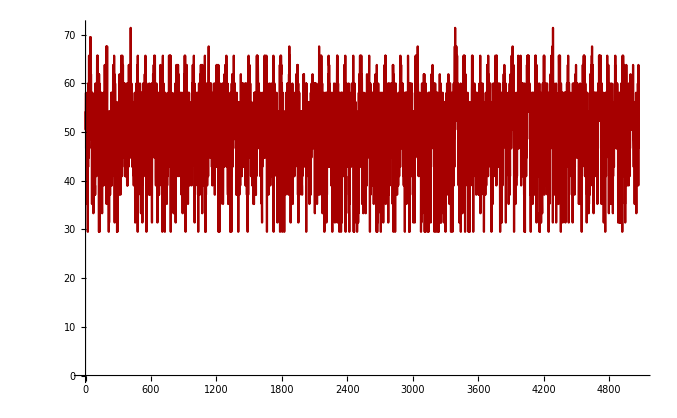

```mathematica
ListLinePlot[test]
```

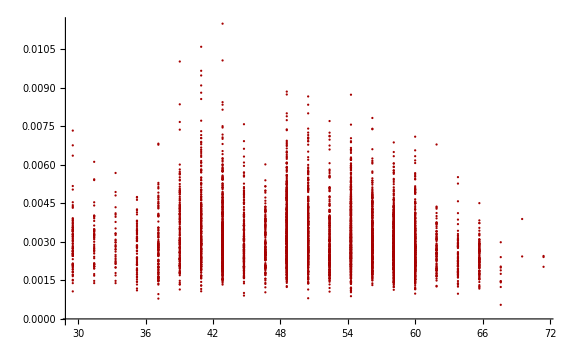

```mathematica
test=Flatten[Table[Map[{#[[1]],#[[3]]}&,centers[[i]]],{i,Length[file]}],1];
ListPlot[test,PlotRange->Full,ImageSize->Large]
```

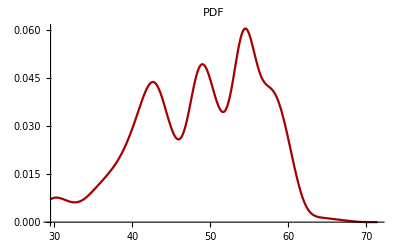
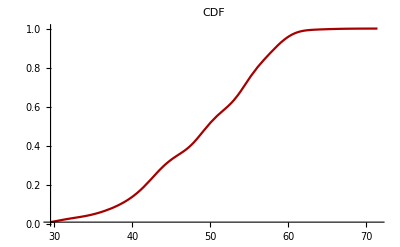

```mathematica
test=Flatten[Table[Map[#[[1]]&,centers[[i]]],{i,Length[file]}],1][[winter]];
𝒟 = SmoothKernelDistribution[test];
Table[Plot[f[𝒟, x], {x, Min[test], Max[test]}, PlotLabel -> f,PlotRange->Full], {f, {PDF, CDF}}]
```

```mathematica
GeoPlot[data_,bounds_]:=Block[{image},
image=ArrayPlot[data,
                 PlotRange->Full,
                 ColorFunction->Hue,
                 Frame->False,
                 PlotRangePadding->None, (* Important *)
                 PlotLegends->Automatic];
Legended[GeoGraphics[
   {{GeoStyling[{"GeoImage", image[[1]]}, 
     GeoRange -> bounds], 
     GeoBoundsRegion[bounds]},  (* image background stretched within bound area *)
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]}},
   GeoProjection ->"Mercator",
   GeoGridLines -> True, 
   GeoRange -> bounds,
   ImageSize -> Medium], 
image[[2]]]]
```